### Estimation of Coupled Exponential Distribution using IAs

Generate Samples using the Type II Pareto Distribution
	To correspond with the variables using for the Coupled Exponential Distribution the following definitions are used  k = σ/κ and α = 1/κ.

```mathematica
CEDSamples[μ_,σ_,κ_,n_]:=
RandomVariate[ParetoDistribution[σ/κ,1/κ,μ],n]
```

```mathematica
CEDSamples011 = CEDSamples[0,1,1,1000]
```

{110.619,3.34353,0.352512,1.27218,0.72279,2.50973,3.44373,2.24702,0.0984341,0.861581,0.90326,1.05731,4.31855,4.92382,8.73819,0.0518892,5.68069,1.11081,3.22734,0.518518,0.957757,0.448917,0.494186,0.550288,0.565967,1.52107,1.58684,0.890482,0.415408,0.387763,78.2175,0.0565014,1.13795,7.54905,0.134186,0.19571,0.327442,0.77353,0.982051,15.6924,1.01789,0.448683,1.35744,0.550426,0.532105,16.458,0.253441,22.0489,11.9489,0.222206,0.58535,1.53759,1.09431,0.121643,0.680264,0.125733,0.0217505,6.96283,0.779472,0.0809803,0.00769632,55.5607,2.29865,0.15829,1.33118,0.345086,8.77281,4.47397,2.46764,0.653981,1.04745,2.99536,0.578347,0.348101,1.00375,0.142996,0.166732,5.54498,0.210433,0.566234,0.309661,3.62984,0.476073,0.0704572,0.632583,0.154965,1.50165,1.26938,4.71514,1.04386,0.098604,13.0637,3.60572,0.230279,0.118765,2.34859,0.820785,3.21713,225.788,1.73227,0.418392,0.542282,0.145521,0.0948014,0.510019,3.94362,1.74995,43.5976,0.557176,0.219254,0.0601545,0.886455,5.96133,2.46419,0.27268,0.119823,19.8421,0.318358,0.0910796,26.5031,22.4511,0.584913,1.50588,0.433324,4.28032,0.214821,1.34032,0.160383,1.80655,0.0792723,0.137991,0.118281,0.407348,1.25438,0.987423,0.879734,1.68844,1.866,0.454528,0.0899095,0.0647079,2.52151,1.77541,16.8399,1.15636,0.340771,0.680417,0.722951,2.31225,0.353022,0.148444,208.816,0.622777,0.19925,1.27772,12.7236,1.6773,0.0252299,4.7876,10.1593,0.104191,3.22694,2.19425,0.527057,1.2767,2.10217,0.259292,2.31718,0.372741,0.802505,3.81221,0.592067,0.370694,1.42311,4.69917,4.68676,0.389443,24.9854,0.0375312,1.69323,3.61212,0.0758923,0.821101,1.31908,1.51479,0.552879,0.835883,0.439968,0.30512,2.25345,13.8693,0.108235,1.31131,2.72627,2.49267,2.15956,2.42821,97.4611,2.84315,0.00913829,2.08777,55.5238,0.147293,0.111088,2.78652,4.0353,0.106403,27.9645,1.79015,193.598,4.52503,0.289447,0.470274,0.109234,1.34069,19.3375,1.22008,8.54196,186.74,0.00908267,0.141615,4.72502,0.0684318,0.374731,0.30914,1.04133,0.130887,0.845044,60.9556,3.21658,12.5886,2.26354,27.6014,11.7066,0.0305953,21.1768,1.38851,0.156544,0.12513,0.664469,0.918192,0.0624399,449.27,1.29076,0.0144527,0.267418,0.0283542,0.248672,5.59968,0.0379609,307.683,0.142881,0.413779,0.100478,2.47814,1.73942,8.90057,1132.78,0.300651,0.399531,2.34796,0.508861,0.238584,0.263296,4.41116,0.0803308,4.22529,1.53407,6.78657,0.028256,0.435177,3.72856,0.473015,1.04037,0.991764,0.214835,9.8639,0.548977,4.34035,0.0729653,0.529596,0.503581,1.09717,13.2904,1.24991,0.162147,1.09367,0.302806,1.20811,0.0717875,0.940613,1.05333,0.0922562,0.881859,9.10361,0.0329125,1.69357,33.8333,1.74901,0.499571,0.98423,0.10474,0.125884,1.83852,0.165999,0.041808,16.5605,0.0946276,12.3168,0.834498,0.268578,9.50898,0.0143223,4.4602,0.352218,1.49351,0.439332,1.82652,1.27822,4.9377,0.207219,0.59125,1.63509,9.73515,0.215064,0.30646,0.242575,15.0957,2.02941,0.335733,0.0160437,0.0673013,7.54964,0.479083,3.82093,23.5393,0.499477,0.179163,0.586248,15.3818,1.37787,1.48617,0.505683,0.342997,0.0761838,7.8675,10.3995,0.954411,0.3149,4.2816,4.06247,0.489836,5.55555,0.0352465,2.05663,1.28157,0.452064,0.978468,0.492747,2.48484,7.6418,0.0761511,0.157075,1.98883,1.59906,0.0389499,0.531656,5.2272,2.83317,0.353957,0.503537,1.56321,0.150274,2.64335,2.34669,0.678199,10.4296,0.47338,0.849161,1.41388,2.18384,1.95394,0.696445,4.97836,10.7202,0.251549,2.768,0.226637,0.0695585,0.263251,0.725847,1.11819,0.263781,0.0280769,29.6485,0.146651,0.446879,10.0604,1.03994,1.68328,0.284997,0.185539,0.234171,0.184798,22.1276,0.646336,0.749947,3.6901,0.375022,1.13042,2.60476,4.22407,1.42586,0.234658,2.83107,1.04449,0.644676,12.2031,1.20974,9.14886,3.65221,1.74937,5.92986,0.0206072,0.32907,1.33939,0.639119,9.23644,0.477368,4.70776,1.93837,0.598751,0.0570094,4723.78,4.95242,0.194109,2.17815,0.620802,0.775496,1.40801,0.748346,1.56968,0.514168,0.394131,4.67792,1.24044,1.96055,2.81097,0.149755,2.04108,41.4593,0.277236,0.845678,6.50638,0.635644,2.56731,0.00925307,0.472722,0.964735,0.460929,3.805,0.521505,0.813123,0.444913,0.64787,0.283613,12.6411,1.26916,0.0233857,1.98295,0.443021,0.485249,0.956814,0.153597,51.1824,0.652426,0.739775,0.123713,0.185606,0.797473,1.10487,0.757093,2.23421,3.9903,0.248478,0.511801,0.248057,0.0590551,8.30064,0.37813,0.768298,0.882335,0.351006,0.126984,1.12751,1.55098,12.0611,9.61702,1.758,0.29136,0.630453,37.5273,0.470737,5.29742,6.4102,0.283937,0.421801,3.25763,0.0833152,0.521066,1.67506,7.02465,0.0335951,0.412154,98.4953,0.0564408,0.434348,1.11135,1.83573,1.56784,4.00346,4.07418,2.04477,0.760009,18.9888,0.14226,0.506664,1.72371,6.9264,0.655604,77.2645,262.605,4.43842,0.687011,1.3332,0.0162657,0.595779,1.05059,2.89338,0.030414,1.45127,0.306383,1.12404,2.61859,0.111698,33.1852,0.303596,0.420318,0.261287,0.0516289,0.0535484,0.130946,0.904676,0.944977,1.08929,38.4629,1.11364,0.822819,0.572359,2.66079,2.22204,0.604926,0.467012,3.59311,0.107304,0.542339,5.57844,1.3411,0.222841,0.404176,5.9581,0.734247,1.12559,0.859368,18.4032,3.1807,1.79313,2.67104,0.273953,0.242828,1.65268,0.206681,1.36515,3.93977,1.25383,16.3395,11.9272,5.55825,3.62901,11.3152,18.7939,49.433,6.93819,0.181483,4.75798,0.229412,25.5857,1.88946,1.12238,9.6538,1.21571,0.621104,0.744612,3.40458,0.51389,0.606205,1.5887,0.160672,2.15848,0.362875,1.13887,0.670976,1.99865,2.61173,0.472902,0.00836221,1.95665,3.08925,0.268707,0.811597,15.1326,0.424175,11.1932,0.517163,2.80938,0.495127,0.173673,25.4434,0.342512,1.5458,4.9571,1.78649,9.28288,0.199618,0.0550884,3.21444,0.481181,1.00658,1.75529,0.206587,1.06476,5.21068,5.05389,0.0117293,0.236216,32.0894,0.305403,1.01404,0.203073,0.948696,0.216705,5.52876,16.0676,0.274673,0.593113,3.92973,1.00818,0.921738,0.0653878,0.409794,1.90052,0.824511,0.0422358,18.4751,0.0915316,0.40558,1.17352,0.0271615,0.00451565,5.51678,0.138329,13.5426,0.151733,2.07329,2.07266,0.616077,0.0540953,0.0629384,2.34059,0.048377,0.556321,1.52003,0.912564,1.29985,0.0277259,18.0905,9.42379,1.0333,4.01258,1.00338,4.38959,0.133091,0.0407531,2.06339,0.358869,0.0799359,3.90583,1.3291,0.917213,0.561057,0.106154,0.0561886,0.262782,3.2046,0.620316,0.865679,5.99181,0.0664118,0.527524,0.752745,0.0608129,3.0455,11.3446,11.1171,1.22992,0.0668965,3.56448,0.154691,4.15986,0.0487292,22.3068,0.854309,0.104861,5.46171,0.903098,23.2751,0.829127,0.213693,0.445422,1.84283,0.0138399,0.849131,4.73379,0.483704,0.305905,0.14298,6.66347,0.0163147,0.267191,0.523175,3.2727,22.7786,5.58044,1.1886,3.12635,0.473384,41.388,0.382679,0.134691,0.521464,0.570665,2.84936,16.0273,0.395783,0.423432,0.588185,8.36962,0.420377,0.0472582,1.73338,1.99963,3.73353,0.551006,0.00283999,0.466216,0.408624,6.15702,0.850364,2.95711,3.48566,0.106147,0.496939,1.28803,53.7219,0.285023,1.25965,0.683753,3.5729,0.132642,1.26461,562.726,2.93812,8.22449,28.54,0.61619,1.73524,1.16077,8.72406,18.3784,0.221206,0.810249,27.0166,1.28896,4.68393,0.179705,0.346113,3.3073,1.61344,1.1456,0.0348208,0.523253,2.20913,7.81614,1.4832,0.908508,5.95972,3.16883,1.15122,0.124408,3.14715,2.26354,1.80293,1.61462,0.758199,4.4873,721.059,2.25894,0.282333,4.0798,1.41737,1.41196,0.103634,0.316007,2.83629,0.0951941,0.59596,2.87376,3.07096,14.8508,2.40921,4.40856,6.50498,0.63743,4.10347,0.2398,1.87344,0.466507,1.59792,1.86027,0.0566228,0.118086,1.43867,2.44605,0.737481,0.182609,2.68859,2.55781,0.390571,0.222869,0.201717,0.342116,0.0445849,0.365112,7.83437,0.267193,0.788364,6.89373,0.110069,0.102879,7.64531,2.43594,0.764528,0.283594,0.341166,0.56592,0.441798,0.91438,0.132456,8.84922,2.78575,0.924715,0.681735,1.42702,0.145716,1.25997,1.26707,74.1191,0.481158,3.40037,0.169829,0.866007,1.21805,0.632151,1.50031,0.233346,0.999004,3.93562,8.26403,1.50945,22.9437,0.102363,0.513547,1.85307,0.32914,0.362266,3.84744,0.35568,1.00864,0.449013,2.87624,0.0558998,3.17438,2.88297,0.404572,0.000288541,2.25316,5.31677,0.0638961,0.176733,0.348487,0.166019,0.316412,0.069751,0.25999,0.784775,3.30651,0.574253,5.89943,0.0998455,4.02274,0.437057,0.694327,0.100255,0.225655,42.3272,1.12414,3.10126,0.588133,2.71455,1.00154,0.806517,1.85507,8.38599,2.08745,2.79634,8.44511,1.93305,0.756391,0.780325,0.0577789,1.19389,3.88614,0.481488,0.104468,1.45895,8.08708,0.578991,2.53363,2.91778,7.0152,4.22314,0.126796,1.17193,5.08895,1.17777,0.212298,0.106188,0.898753,1.98062,4.19683,0.436968,0.124874,0.443172,0.191857,0.0404309,0.71292,8.25021,0.178143,0.32761,3.2657,9.70759,0.624834,0.257757,0.0957696,0.55386,3.2633,3.03871,0.556384,0.462146,10.1194,0.103566,1.25126,24.8069,3.0878,4.47998,0.00875004,4.31094,0.472793,2.84627,2.07604,6.97023,1.4794,0.0959353,0.32396,26.5092,0.224924,3.46917,1.5709,8.68624,2.24024}

Plot the pairs

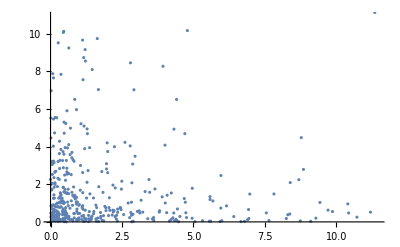

```mathematica
ListPlot[Partition[CEDSamples011,2]]
```

Estimate the mean

```mathematica
EstimateCRVMean[CEDSamples011,{},{},{},
"iterations"-><|"iterateXeqX"->2,"iterateRec"->10|>,
"saveXeqX"->False]
```

<|lowestVariability→{0.4920.025,492},lowestVarNearEnd→{0.530.04,1996},firstLast→{{0.50.5,254},{0.520.05,2466}},minMax→{{0.50.5},{0.540.05}},sampleRange→0.1,allEst→{0.474911,0.509613,0.533948,0.600344,0.571211,0.533623,0.481496,0.52066,0.446783,0.503839},allCombinedEsts→{{0.50.5,254},{0.4920.025,492},{0.5060.030,724},{0.530.05,972},{0.540.05,1252},{0.540.04,1500},{0.530.05,1748},{0.530.04,1996},{0.520.05,2224},{0.520.05,2466}},XeqX→{}|>